-x^2/2+x^4/4

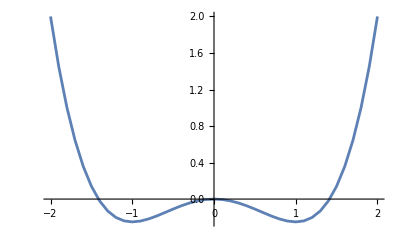

```mathematica
Clear["Global`*"]
	Potential[x_] = x^4 /4 - x^2 /2
	PotentialPlotData = Table[{x,Potential[x]}, {x,-2,2,0.1}];
	ListLinePlot[PotentialPlotData]
```

```mathematica
totEnergy[x_]:=m /2 (dx/dt)^2+Potential[x]==e;
totEnergy[x];
dTsol=Solve[totEnergy[x],dt];
dTsol1=dTsol/. {{{x0_},{y0_}}->{x0,y0}};
dTime=dTsol1[[2]]/.{m->1};
dt/. dTime
```

(√2 dx)/(√(4 e+2 x^2-x^4))

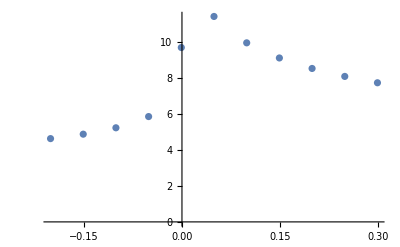

```mathematica
data = {};
For[i = -0.201, i <= 0.301, i = i + 0.05,
 ExtreamasNegative =SolveValues[Potential[x]==i,x, Reals][[{1,2}]]; 
TimePeriod2 = 2 NIntegrate[(√2)/(√(4  i +2 x^2-x^4)), {x,ExtreamasNegative[[1]] , ExtreamasNegative[[2]]}];
AppendTo[data,{i,TimePeriod2}]]
ListPlot[data, PlotRange->Automatic]
```

x-x^3

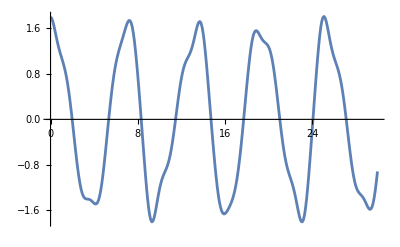
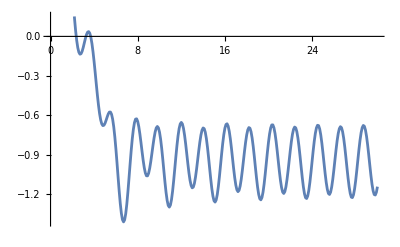
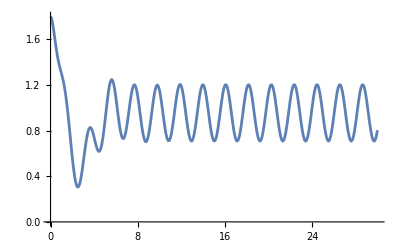
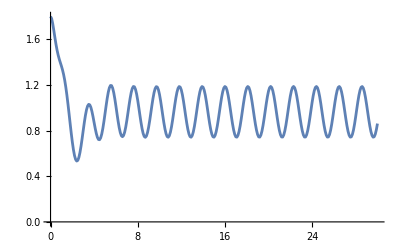

```mathematica
Force[x_] =- D[Potential[x],{x,1}]
plts = {};
For[i =0, i <=3,i++, 
eqn := {x''[t] == Force[x[t]] + A Sin[ 2 ω t] - γ x'[t] ,x[0] ==18/10, x'[0] == 0 } /. {A -> 2, ω -> 1.5 , γ -> 6*i/10};
soln  = NDSolve[eqn,x[t],{t,0,100}];
data  = Table[{t,  x[t] /. Flatten[soln]} , {t,0,30,0.1}];
plt = ListLinePlot[data];
AppendTo[plts,plt];
]
plts
```